```mathematica
var[c1_,c2_,col_]:=Style[Subscript[Style[c1,Italic],c2],col];
```

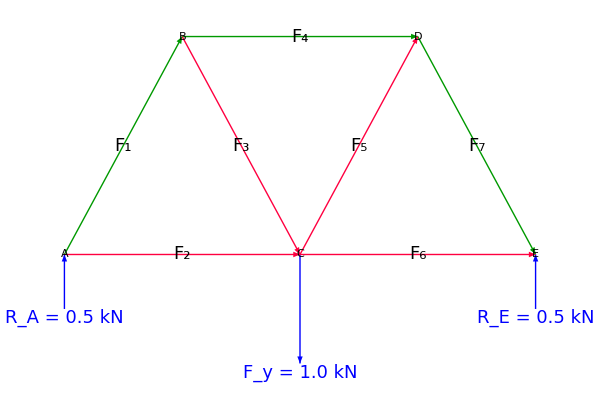

```mathematica
Module[{w,h,θ,Fy,sol,RA,RE,colC,colT},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;

sol=Quiet@Solve[N@{w*Fy-2*w*re==0,ra-Fy+re==0},{ra,re}][[1]];
RA=ra/.sol;RE=re/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
{Blue,Arrow[{{0,-0.25*h},{0,0}}],Arrow[{{w,0},{w,-0.5*h}}],Arrow[{{2*w,-0.25*h},{2*w,0}}],
Text[Style[Row@{var["F","y",Blue]," = ",NumberForm[Fy,{2,1}]," kN"},18,Blue],{w,-0.5*h},{0,1.5}],
Text[Style[Row@{var["R",#1,Blue]," = ",#2," kN"},18,Blue],#3,{0,1.5}]&@@@{{"A",RA,{0,-0.25*h}},{"E",RE,{2*w,-0.25*h}}}},

{colC,(*Arrowheads@{-0.05,0.05},*)Arrowheads@{{-0.05,0.05},{0.05,0.95}},
Arrow[{{0,0},{0.5*w,h}}],Arrow[{{0.5*w,h},{1.5*w,h}}],Arrow[{{1.5*w,h},{2*w,0}}]},

{colT,Arrowheads@{{0.05,0.275},{-0.05,0.725}},
Arrow[{{0,0},{w,0}}],Arrow[{{0.5*w,h},{w,0}}],Arrow[{{w,0},{1.5*w,h}}],Arrow[{{w,0},{2*w,0}}]},

(*Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{"AB",{0.25*w,0.5*h}},{"AC",{0.5*w,0}},{"BC",{0.75*w,0.5*h}},{"BD",{w,h}},{"CD",{1.25*w,0.5*h}},{"CE",{1.5*w,0}},{"DE",{1.75*w,0.5*h}}}*)

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{1,{0.25*w,0.5*h}},{2,{0.5*w,0}},{3,{0.75*w,0.5*h}},{4,{w,h}},{5,{1.25*w,0.5*h}},{6,{1.5*w,0}},{7,{1.75*w,0.5*h}}},

Text[Framed[Style[Row@{" ",#1," "},15],Background->White,RoundingRadius->15],#2]&@@@{{"A",{0,0}},{"B",{0.5*w,h}},{"C",{w,0}},{"D",{1.5*w,h}},{"E",{2*w,0}}}
},ImageSize->{600,400}]
]
```

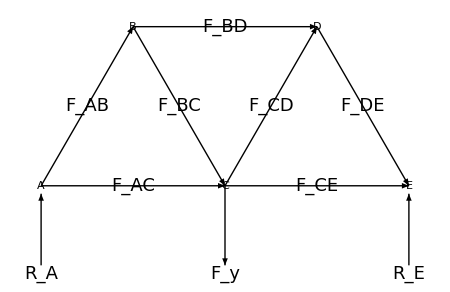

```mathematica
Module[{w,h,θ,Fy,δ,sol,RA,RE},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;δ=0.5*h;

sol=Quiet@Solve[N@{w*Fy-2*w*re==0,ra-Fy+re==0},{ra,re}][[1]];
RA=ra/.sol;RE=re/.sol;

Graphics[{Thick,
Arrowheads@0.05,Arrow[{{0,-δ},{0,-0.05*h}}],Arrow[{{w,0},{w,-δ}}],Arrow[{{2*w,-δ},{2*w,-0.05*h}}],
Text[Style[var["F","y",Black],18],{w,-δ},{0,1.5}],
Text[Style[var["R",#1,Black],18],#3,{0,1.5}]&@@@{{"A",RA,{0,-δ}},{"E",RE,{2*w,-δ}}},

{Arrowheads@{{-0.05,0.05},{0.05,0.95}},
Arrow[{{0,0},{0.5*w,h}}],Arrow[{{0.5*w,h},{1.5*w,h}}],Arrow[{{1.5*w,h},{2*w,0}}]},

{Arrowheads@{{0.05,0.275},{-0.05,0.725}},
Arrow[{{0,0},{w,0}}],Arrow[{{0.5*w,h},{w,0}}],Arrow[{{w,0},{1.5*w,h}}],Arrow[{{w,0},{2*w,0}}]},

(*Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{1,{0.25*w,0.5*h}},{2,{0.5*w,0}},{3,{0.75*w,0.5*h}},{4,{w,h}},{5,{1.25*w,0.5*h}},{6,{1.5*w,0}},{7,{1.75*w,0.5*h}}},*)
Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{"AB",{0.25*w,0.5*h}},{"AC",{0.5*w,0}},{"BC",{0.75*w,0.5*h}},{"BD",{w,h}},{"CD",{1.25*w,0.5*h}},{"CE",{1.5*w,0}},{"DE",{1.75*w,0.5*h}}},

Text[Framed[Style[Row@{" ",#1," "},16],Background->White,RoundingRadius->15,FrameMargins->Small],#2]&@@@{{"A",{0,0}},{"B",{0.5*w,h}},{"C",{w,0}},{"D",{1.5*w,h}},{"E",{2*w,0}}}
},ImageSize->450]
]
```